# CLIMATE RISKS

## Land use planning in the least developed countries to mitigate the consequences of climate change By Sybille Roemer, Thanusya Thambirajah & Yanis Cuche

## CONTEXT

2030, it is the year announced in the latest IPCC report (2022) when the fateful 1.5°C limit target set by the Paris Agreement will be reached (1). This is much earlier than expected, and the projected trajectory is now in the order of 4 to 5°C. The link between human activity and global warming is no longer disputed, as is the link between global warming and increases in the frequency and intensity of natural disasters, like heat waves, floods, sea level rise, etc. All these phenomena tend to get worse, with disastrous consequences for human infrastructures, air quality, loss of biodiversity, an so on.

Not all countries are equally affected by global warming, and it is often the poorest countries that suffer the most severe consequences. Every region of the world is affected, but at different scales, and it is unfairly the countries that pollute the least that are most affected. Globally, the countries of the South are far more vulnerable than the countries of the North, experiencing more water and food shortages, and increasingly extreme temperatures. Climate risks are highly location-specific.

In this project, we will first try to predict the climate risks associated with the regions of underdeveloped countries, using the database of least developed countries (UNCTAD (2)) as well as the database on climate risks (TruCost). As a second step, we will identify the least climate risky places, with the aim of building new infrastructures or reinforcing them according to their future climate risks.

UNCTAD : Least Developed Countries (46 countries)

```mathematica
Import["https://unctad.org/sites/default/files/inline-images/2022-ldc_report_ldc_map_1200.png"]
```

-Graphics-

Sources
(1) : https://siltmedia.com/giec-rapport-resume-complet/
(2) : https://unctad.org/topic/least-developed-countries/list

## DATA CLEANING

Importation of the dataset of TruCost already containing only the least developed countries

```mathematica
dataRaw = Import["https://raw.githubusercontent.com/thanusya/DSML_project/main/TruCost_EDX_Physical_Least-Developed.csv", "Dataset", HeaderLines -> 1];
```

```mathematica
Dimensions[dataRaw]
```

{2746,309}

The dataset contains 2746 observations and 309 different variables.

Here are the different Facility Category.

```mathematica
DeleteDuplicates@dataRaw[All,"Facility Category"]
```

Here are the different countries in the dataset.

```mathematica
Countries=Normal@dataRaw[All,"Country"];
```

```mathematica
CountryWithoutDup=Sort@DeleteDuplicates@Countries
```

{Angola,Benin,Burkina Faso,Cambodia,Chad,Djibouti,Eritrea,Ethiopia,Gambia,Guinea,Guinea-Bissau,Haiti,Kiribati,Laos,Liberia,Madagascar,Malawi,Mali,Mauritania,Mozambique,Myanmar,Niger,Rwanda,Senegal,Sierra Leone,Solomon Islands,Sudan,Tanzania,Timor-Leste,Togo,Uganda,Yemen,Zambia}

Here are the countries that are part of the least developed countries, but are unfortunately not part of the Trucost dataset.

```mathematica
ListcountriesUNCTAD = Sort@{"Angola","Benin", "Burkina Faso", "Burundi", "Central African Republic", "Chad", "Comors","Democratic Republic of the Congo", "Djibouti", "Eritrea", "Ethiopia", "Gambia", "Guinea", "Guinea-Bissau", "Lesotho", "Liberia", "Madagascar","Malawi", "Mali", "Mauritania", "Mozambique", "Niger", "Rwanda", "Sao Tome and Principe", "Senegal", "Sierra Leone", "Somalia", "South Sudan", "Sudan", "Togo", "Uganda", "Tanzania","Zambia", "Afghanistan", "Bangladesh", "Bhutan", "Cambodia", "Laos", "Myanmar", "Nepal","Timor-Leste", "Yemen", "Haiti", "Kiribati", "Solomon Islands", "Tuvalu"};
```

```mathematica
DeleteCases[ListcountriesUNCTAD, Alternatives @@ CountryWithoutDup]
```

{Afghanistan,Bangladesh,Bhutan,Burundi,Central African Republic,Comors,Democratic Republic of the Congo,Lesotho,Nepal,Sao Tome and Principe,Somalia,South Sudan,Tuvalu}

In the Trucost Climate Change Physical Risk Analytics dataset, the seven climate risk, that are considered, are Water Stress, Flood, Heatwave, Cold wave, Hurricane, Wildfire and Sea Level Rise. In the case of this project, the focus will be put on the composite variable that is intended to provide a combined measure of company exposure to all seven climate change physical risk indicators.

```mathematica
Normal @Keys[dataRaw[1]];
```

```mathematica
compositekeys = Normal@Keys[dataRaw[1]][[275;;306]];
```

The focus is on 2040, as building or renovating a building can take many years. Beyond 25 years, the building will have to be renovated, therefore current constructions must be concerned about the risks in 2040.

```mathematica
data2040=dataRaw[All, {"Country","Latitude","Longitude","Facility Category","ExposureScore_Composite_High_2040","ExposureScore_Composite_Low_2040","ExposureScore_Composite_Moderate_2040","ExposureScore_Composite_ModerateHigh_2040"}];
```

```mathematica
compositekeys2040 = Normal @ compositekeys[[{3,11, 19,27}]]
```

{ExposureScore_Composite_Low_2040,ExposureScore_Composite_Moderate_2040,ExposureScore_Composite_ModerateHigh_2040,ExposureScore_Composite_High_2040}

Here, Low, Moderate, Moderate High, and High represent the different RCP scenarios. 
Note: The four RCP (Representative Concentration Pathway) scenarios are used to model future climate change. They were developed by the Intergovernmental Panel on Climate Change (IPCC) and are used to estimate future greenhouse gas concentrations and their associated impacts on the climate system. The four RCP scenarios are: RCP2.6, RCP4.5, RCP6.0 and RCP8.5. RCP2.6 is the most ambitious scenario, aiming to limit global warming to 2°C above pre-industrial levels by 2100. RCP4.5 is a moderate scenario, aiming to limit global warming to 2°C above pre-industrial levels by 2100. RCP6.0 is an intermediate scenario, aiming to limit global warming to 3°C above pre-industrial levels by 2100. RCP8.5 is the most extreme scenario, aiming to limit global warming to 4°C above pre-industrial levels by 2100.

```mathematica
Risks2040={"ExposureScore_Wildfire_High_2040","ExposureScore_ExtremeCold_High_2040","ExposureScore_ExtremeHeat_High_2040","ExposureScore_WaterStress_High_2040","ExposureScore_CoastalFlood_High_2040","ExposureScore_RiverineFlood_High_2040","ExposureScore_TropicalCyclone_High_2040","ExposureScore_Drought_High_2040","ExposureScore_Composite_High_2040"};
```

The missing values are removed from the dataset.

```mathematica
dataClean2040=Select[data2040, FreeQ[#,""]&];
```

## DATA VISUALIZATION

Data visualization enable the exploration of the dataset and the visualization of the analytics. Therefore, the difficult concepts and the patterns are easier to define.

These maps allow the visualization and comparison of selected countries to determine which are most/least exposed to composite risks over time. The maps can be manipulate to have the different years and the different RCP scenarios.

```mathematica
countryEntities = Interpreter["Country"][#] & /@ Countries;
```

```mathematica
Manipulate[
GeoRegionValuePlot[ 
AssociationThread[countryEntities, Normal@dataRaw[All,choice]],
ColorFunction -> "TemperatureMap",PlotLabel->"Countries Exposure to composite risks"],
{choice,compositekeys}]
```

For example, in 2020, considering a low RCP scenario, the countries at high risk are Yemen and Ethiopia.

These bar charts allow a ranking of the selected countries and to see which ones are most exposed to the composite risk. The bar charts can be manipulate to have the different years and the different RCP scenarios.

```mathematica
Manipulate[
BarChart[
Sort@Select[
AssociationThread[countryEntities, Normal@dataRaw[All,choice]],
#>Mean[
AssociationThread[countryEntities, Normal@dataRaw[All,choice]]]&],ChartStyle->66, ChartLegends->Keys@AssociationThread[countryEntities, Normal@dataRaw[All,choice]]],{choice, compositekeys}]
```

This box plot shows the climate risks to which the selected countries are most exposed in 2040 under high RCP scenario.

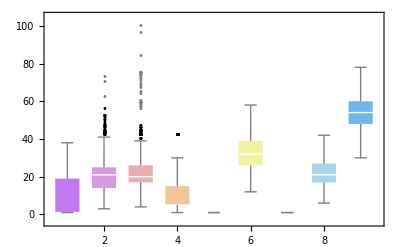

```mathematica
BoxWhiskerChart[Normal@dataRaw[All,#]& /@Risks2040,  "Outliers",
                                                      ChartLegends ->Risks2040, 
                     ChartStyle->"Pastel", ChartLabels -> 
  Style["Current Temperature of the Largest Cities in Japan", "Title",
    14]]
```

The graph shows that in our subset of countries, the highest risk exposure is on average river flooding.

Here is the correlation matrix between the different climate risks in 2040 for the high RCP scenario.

```mathematica
Risks2040corr={"ExposureScore_Wildfire_High_2040","ExposureScore_ExtremeCold_High_2040","ExposureScore_ExtremeHeat_High_2040","ExposureScore_WaterStress_High_2040","ExposureScore_RiverineFlood_High_2040","ExposureScore_TropicalCyclone_High_2040","ExposureScore_Drought_High_2040","ExposureScore_Composite_High_2040"};
```

The coastal flood has been removed as it contained only 5 values.

```mathematica
datarisks2040=dataRaw[All, Risks2040corr];
```

```mathematica
datarisksClean2040=Select[datarisks2040, FreeQ[#,""]&];
```

```mathematica
corrMatrix=Correlation[Normal @datarisksClean2040[All,Risks2040corr][Values]];
```

```mathematica
corrMat =Dataset[AssociationThread[Risks2040corr->(AssociationThread[Risks2040corr->#]&/@Round[corrMatrix,0.01])]]
```

```mathematica
MatrixForm[Round[corrMatrix,0.01]]
```

(1. | 0.13 | -0.12 | -0.23 | -0.04 | 0.07 | 0.28 | 0.18
0.13 | 1. | -0.52 | -0.23 | 0.06 | -0.12 | -0.04 | -0.04
-0.12 | -0.52 | 1. | 0.43 | -0.15 | 0.31 | -0.19 | 0.42
-0.23 | -0.23 | 0.43 | 1. | 0.13 | -0.02 | -0.39 | 0.83
-0.04 | 0.06 | -0.15 | 0.13 | 1. | -0.16 | -0.23 | 0.35
0.07 | -0.12 | 0.31 | -0.02 | -0.16 | 1. | 0.01 | 0.09
0.28 | -0.04 | -0.19 | -0.39 | -0.23 | 0.01 | 1. | -0.17
0.18 | -0.04 | 0.42 | 0.83 | 0.35 | 0.09 | -0.17 | 1.)

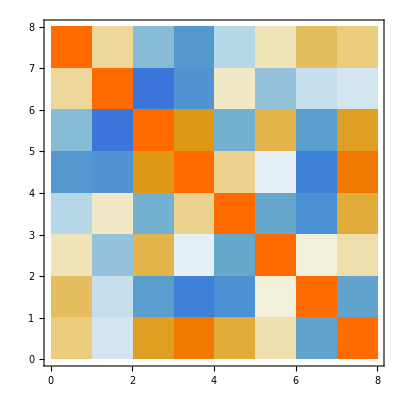

```mathematica
MatrixPlot[corrMatrix]
```

The composite is highly correlated with the water stress risk, which means that it has an important impact on the regions of our dataset.

The objective of the project is to forecast and plan land use to reduce the risk of climate damage. To get a better idea of the type of activities in the database, here is a pie chart:

```mathematica
other =Total@Values@Select[Sort@Counts@dataRaw[All, "Facility Category"],#<10&];
```

```mathematica
facilitynumber=Sort@Dataset@Append[Normal@Select[Sort@Counts@dataRaw[All, "Facility Category"],#>10&],"Other" ->other ];
```

```mathematica
PieChart[
facilitynumber,  
ChartLabels ->Placed[Automatic,"VerticalCallout"],
ChartStyle -> "DarkRainbow"]
```

-Graphics-

Most of the facilities are financial institutions, this information is important as the planning of the land use of the project will mainly predict the climate risk for financial institutions.

## PREDICTION

First, the data will be divided our data into two subset. The first one is the training set (80% of our observations) on which we will train our models and the second one is the test set. The test set will be used to assess the performance of our predictor.

```mathematica
{trainingset,testset}=TakeDrop[RandomSample[
dataClean2040[All,{"Country","Latitude","Longitude","Facility Category","ExposureScore_Composite_High_2040"}]],
Round[Dimensions[dataClean2040[All,{"Country","Latitude","Longitude","Facility Category","ExposureScore_Composite_High_2040"}]][[1]]*0.8,1]];
```

#### Prediction with different methods

Here is the creation of the predictor using the Wolfram built-In Predict Function. Different predictor with the following methods: Linear regression, RandomForest, Nearest Neighbors and Decision Tree, have been created.

```mathematica
{linearPred,gkNNPred, randomforestPred,decisionTreePred} = 
 Predict[trainingset->"ExposureScore_Composite_High_2040", Method ->#] & /@ {"LinearRegression", "NearestNeighbors", "RandomForest", "DecisionTree"};
```

Once the predictors are built, the test set will assess their performance.

```mathematica
PredictorMeasurements[#, testset]&/@{linearPred,gkNNPred, randomforestPred,decisionTreePred};
```

Based on these results, the Nearest Nearest Neighbors is the most accurate one. Since some of the input variables of the model are geo-data, the results are coherent.

### Prediction of the different RCP with kNN methods

The first step is the creation of a list used for the predicted variables later on. As explained above, the interest is put on the risk composite score in the different RCP scenario (High, Moderate-High, Moderate and low).

```mathematica
variableToPredict={"ExposureScore_Composite_High_2040","ExposureScore_Composite_ModerateHigh_2040","ExposureScore_Composite_Moderate_2040","ExposureScore_Composite_Low_2040"};
```

```mathematica
Basevariable={"Country","Latitude","Longitude","Facility Category"};
```

Creation of the train and test set.

```mathematica
{trainingset,testset}=
TakeDrop[
RandomSample[
dataClean2040[All,{"Country","Latitude","Longitude","Facility Category","ExposureScore_Composite_High_2040","ExposureScore_Composite_ModerateHigh_2040","ExposureScore_Composite_Moderate_2040","ExposureScore_Composite_Low_2040"}]],
Round[
Dimensions[
dataClean2040[All,{"Country","Latitude","Longitude","Facility Category","ExposureScore_Composite_High_2040","ExposureScore_Composite_ModerateHigh_2040","ExposureScore_Composite_Moderate_2040","ExposureScore_Composite_Low_2040"}]]
[[1]]*0.8,1]];
```

```mathematica
p = Predict[trainingset[All, Flatten@{#,Basevariable}]->#, Method ->"NearestNeighbors"] & /@ variableToPredict;
```

Once the predictors are built, the test set will assess their performance.

```mathematica
PredictorMeasurements[p[[#]], testset[All, Flatten@{variableToPredict[[#]],Basevariable}]]&/@Range[Length@p];
```

## CLASSIFICATION

Since it can be difficult to assess a number, the risk values have been assigned to categorical classes (low, moderate low, moderate high and high).

Extraction of the risk variable in forms of a list for all scenario and the latitude longitude variable

```mathematica
{CompositeHigh2040, CompositeModerateHigh2040,CompositeModerate2040, CompositeLow2040}=Normal@dataClean2040[All,#]&/@variableToPredict;
```

```mathematica
{listLat, listLong}=Normal@dataClean2040[All,#]&/@{"Latitude","Longitude"};
```

Creation of function that replace number into categorical values

```mathematica
ChangeHigh[x_]:=x/. n_?NumericQ /; n >75 -> "High"
```

```mathematica
ChangeModerateHigh[x_]:=x/. n_?NumericQ /; 50<n ≤75 -> "Moderate High"
```

```mathematica
ChangeModerateLow[x_]:=x/. n_?NumericQ /;25<n≤50 -> "Moderate Low"
```

```mathematica
ChangeLow[x_]:=x/. n_?NumericQ /; n ≤25 -> "Low"
```

Application of the above created function on the extracted risks lists

```mathematica
{CategoricalHigh2040,CategoricalModerateHigh2040, CategoricalModerate2040, CategoricalLow2040}=ChangeHigh@ChangeModerateHigh@ChangeModerateLow@ChangeLow[#]&/@{CompositeHigh2040, CompositeModerateHigh2040,CompositeModerate2040, CompositeLow2040};
```

Creation of a list containing sublist of pair of {lat, long}

```mathematica
LatLong ={listLat[[#]], listLong[[#]]} & /@ Range[Length@listLat];
```

```mathematica
{CatdataHigh,CatdataModerateHigh, CatdataModerate, CatdataLow}=Normal@AssociationThread[LatLong,#]&/@{CategoricalHigh2040,CategoricalModerateHigh2040, CategoricalModerate2040, CategoricalLow2040}
```

### Creation of multiple classifier with RCP 8.2 (high) and different methodology

As, before for prediction, training set and test set will be created for building the classifier.

```mathematica
{trainH,testH}=TakeDrop[RandomSample[CatdataHigh],Round[Dimensions[CatdataHigh][[1]]*0.8,1]];
```

Creation of the classifier with different methods.

```mathematica
c =Classify[trainH, Method->#]&/@ {"LogisticRegression", "NearestNeighbors", "RandomForest", "DecisionTree"};
```

Displaying of information about the classifiers.

```mathematica
Information[c[[#]]]&/@Range[Length@c];
```

Based on these results, the Nearest Nearest Neighbors is once again the best method to build a classifier with.

Assessment of the performance of the classifier with the test set.

```mathematica
ClassifierMeasurements[c[[#]],testH]&/@Range[Length@c];
```

### Creation of classifier using kNN method for all RCP scenario

As, before for prediction, training set and test set will be created for building the classifier.

```mathematica
{trainMH,testMH}=TakeDrop[RandomSample[CatdataModerateHigh],Round[Dimensions[CatdataModerateHigh][[1]]*0.8,1]];
{trainM,testM}=TakeDrop[RandomSample[CatdataModerate],Round[Dimensions[CatdataModerate][[1]]*0.8,1]];
{trainL,testL}=TakeDrop[RandomSample[CatdataLow],Round[Dimensions[CatdataLow][[1]]*0.8,1]];
{trainH,testH}=TakeDrop[RandomSample[CatdataHigh],Round[Dimensions[CatdataHigh][[1]]*0.8,1]];
```

```mathematica
trainList={trainH, trainMH, trainM, trainL};
testList={testH, testMH, testM, testL};
```

Creation of the classifier for all RCP scenarios.

```mathematica
c={RCPH,RCPMH,RCPM,RCPL} =Classify[#, Method->"NearestNeighbors"]&/@{trainH, trainMH, trainM, trainL};
```

```mathematica
Information[c[[#]]]&/@Range[Length@c];
```

Assessment of the performance of the classifier with the test set.

```mathematica
ClassifierMeasurements[c[[#]],testList[[#]]]&/@Range[Length@c];
```

These results reveal an imbalance between classes. Hence accuracy might not be appropriate to assess the performance of the classifiers. In this case, the use of precision and recall formula will be used.

```mathematica
precision=ClassifierMeasurements[c[[#]],testList[[#]]]["Precision"]&/@Range[Length@c];
```

Average precision across RCP scenarios classifications for the class "High" risks

```mathematica
Mean[precision[[#]][[1]]&/@Range[Length@precision]]
```

0.759371

Average precision across RCP scenarios classifications for the class "Moderate high" risks

```mathematica
Mean[precision[[#]][[3]]&/@Range[Length@precision]]
```

0.947556

Average precision across RCP scenarios classifications for the class "Moderate low" risks

```mathematica
Mean[precision[[#]][[4]]&/@Range[Length@precision]]
```

0.826885

The precision shows the proportion of correctly predicted value for a given class that are true positive.

```mathematica
recall=ClassifierMeasurements[c[[#]],testList[[#]]]["Recall"]&/@Range[Length@c];
```

Average recall across RCP scenarios classifications for the class "high" risks

```mathematica
Mean[recall[[#]][[1]]&/@Range[Length@recall]]
```

0.846034

Average recall across RCP scenarios classifications for the class "Moderate high" risks

```mathematica
Mean[recall[[#]][[3]]&/@Range[Length@recall]]
```

0.939566

Average recall across RCP scenarios classifications for the class "Moderate low" risks

```mathematica
Mean[recall[[#]][[4]]&/@Range[Length@recall]]
```

0.855989

The recall refers to the percentage of total relevant results correctly classified.

## WEBFORM

Here is the deployment of the classifier in the cloud.

```mathematica
AssocRCP=AssociationThread[{"High (RCP 8.5)","Moderate High (RCP 6.0)", "Moderate (RCP 4.5)", "Low (RCP 2.6)"},{RCPH, RCPMH,RCPM, RCPL}];
```

```mathematica
FormLongLatRcp=FormFunction[
   {
   {"RCP","Choose your RCP scenario"}->{"High (RCP 8.5)","Moderate High (RCP 6.0)", "Moderate (RCP 4.5)", "Low (RCP 2.6)"},
   {"lat","Latitude"} -><|"Interpreter" -> "Number","Hint" -> "Enter the latitude of your location" |>,{"long","Longitude"}-><|"Interpreter" -> "Number","Hint" -> "Enter the longitude of your location" |>} ,
   AssocRCP[#RCP][{#lat, #long}]
    &, AppearanceRules -> <|"Title" -> "Climate risk predictor for least developed countries", 
    "Description" -> 
     "Based on the Trucost database, the composite variable contains the risks of water stress, floods, heat waves, cold waves, hurricanes, forest fires, and sea level rise for 2040. Please enter the parameters of your location to see the associated risk."|>];
```

```mathematica
FormLongLatRcp[]
```

Moderate High

```mathematica
CloudDeploy[FormLongLatRcp, "WebServices/FormLongLatRCP", Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/thanusya.thambirajah/WebServices/FormLongLatRCP]